```mathematica
generalreal = {};
generalimag = {};
Msdata = {};
alphadata = {};
DHdata = {};
final = 5000;

For [i = 0, i<final, i++,{
Ms =  RandomReal[{400 10^3,2000 10^3}]; 
xpower = RandomReal[{-4.0,-1.3010}] ;
alpha0 = 10^(xpower) ;
(*DH =  RandomReal[{10^6,100 10^6}];*)
DH = 0;
Clear[θ,HH0,m];
u={1,0,0};
Ku1=0;
Kc1=0;
phiH = 0 π/4;
thetaH = π/2;
ht=0;
hp=1Exp[I w t];
H0 =HH0 Tesla /mu0;
Joule=1; Meter=1; Ampere=1;
Second=1; 
w = 2π f;
Tesla=Joule/Ampere /Meter^2;
γ = 2 π 28 10 ^9/(Tesla Second) ; (* In radians *)
mu0 = 4 π 1 10^-7 Joule/Ampere^2/Meter;
(* Zeeman *)
Ez = -mu0 Ms H0 (Sin[θ] Sin[thetaH] Cos[ϕ - phiH] + Cos[θ] Cos[thetaH]);
(* Uniaxial Anisotropy *)
m= {Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
Eu = -Ku1 (Dot[u,m])^2;
(* Cubic Anisotropy *)
Ea = Kc1/4 (Sin[θ]^4 Sin[2 ϕ]^2 + Sin[2  θ]^2);
(* Demag field *)
Edem = mu0 Ms^2/2 Cos[θ]^2;
Etot= Ez+Edem+Eu+Ea;
Ft =Evaluate[-D[Etot,θ]/Ms];
Fp =Evaluate[-(D[Etot ,ϕ]/Ms)/.θ->Pi/2];
Ftt :=Evaluate[Abs[D[Ft ,θ]]];
Fpp :=Evaluate[Abs[D[Fp ,ϕ]]];
θ= π/2;
α = alpha0+DH/f;
DD = (Ftt -ⅈ w/γ α)(Fpp -ⅈ w/γ α)-(w/γ)^2;
dtheta = 1/DD ((Fpp-ⅈ w/γ α) ht  + ⅈ w/γ α hp);
dphi[Ms_,HH0_,f_,ϕ_]:=Evaluate[ 1/DD ((Ftt-ⅈ w/γ α) hp -ⅈ w/γ α ht)];
Pmag =-f Im[mu0 w /2 Conjugate[ht] dtheta + Conjugate[hp] dphi[Ms,HH0,f,ϕ]];
Pmag1 =-f Re[mu0 w /2 Conjugate[ht] dtheta + Conjugate[hp] dphi[Ms,HH0,f,ϕ]];

ϕ0=N[phiH];
ATable={};
ATable2={};
gr1={};
gr2={};
f=ff*10^9;
For [HH0=.4,HH0>=0.004,HH0-=0.004,{
Sol = Last[FindMinimum[Etot ,{ ϕ, ϕ0},AccuracyGoal->5]];
ϕ0=Mod[180(ϕ/.Sol)/π +180, 360]-180;

AA1=-Simplify[Pmag/.{ ϕ ->ϕ0,t->1},f>0];
AA2=-Simplify[Pmag1/.{ ϕ -> ϕ0,t->1},f>0];
f0 = 1/(2 π) γ Sqrt[Fpp Ftt/(1+α^2)] /. {ϕ -> ϕ0,Ms->500 10^3};
AppendTo[ATable,{HH0,ϕ0}];
AppendTo[ATable2,{HH0,f0}];
g1=Table[{HH0,ff,AA1}, {ff ,.1 ,20,.1 }];
AppendTo[gr1,Evaluate[g1]];
g2=Table[{HH0,ff,AA2}, {ff ,.1 ,20,.1  }];
AppendTo[gr2,Evaluate[g2]];

}];

gr11=Flatten[gr1,1];
gr21=Flatten[gr2,1];
gr12=Flatten[Transpose[gr1],1];
gr22=Flatten[Transpose[gr2],1];

AppendTo[generalreal, gr11];
AppendTo[generalimag, gr21];
AppendTo[Msdata, Ms];
AppendTo[alphadata,xpower];
AppendTo[DHdata,DH];
nombase1 = "data_re_5000/data_real_";
nombase2 = "data_im_5000/data_imgi_";
nomarxiu=nombase1<>ToString[i]<>".csv";
nomarxiu2=nombase2<>ToString[i]<>".csv";
Export[nomarxiu,gr11,"Table"];
Export[nomarxiu2,gr21,"Table"];

}]

Export["Ms_data_5000.csv", Msdata, "Table"];
Export["a_data_5000.csv", alphadata, "Table"];
Export["DH_data_5000.csv", DHdata, "Table"];
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

General::stop: Further output of FindMinimum::fmgz will be suppressed during this calculation.

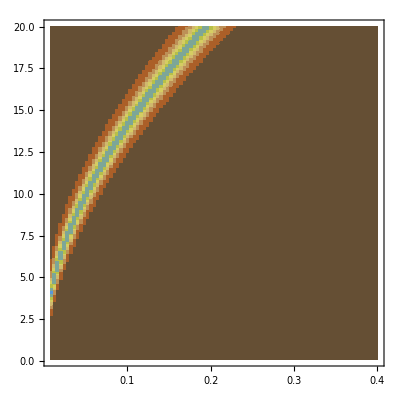

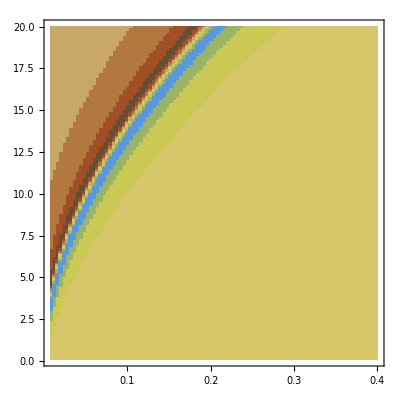

```mathematica
ListContourPlot[gr11,PlotRange->All,Mesh->None,InterpolationOrder->0,ColorFunction->"SouthwestColors"]
ListContourPlot[gr21,PlotRange->All,Mesh->None,InterpolationOrder->0,ColorFunction->"SouthwestColors"]
```

```mathematica
A = ArrayReshape[generalimag, {19800,3,100}];
Dimensions[A];
Export["data/patata2.csv", generalimag, "CSV"]
```

data/patata2.csv

```mathematica
Export["data_real.csv",generalreal,"Table"];
Export["data_im.csv",generalimag,"Table"];
Export["Ms_data.csv", Msdata, "Table"];
```

$Aborted

$Aborted

```mathematica
asd
```

```mathematica
nombreBase="archivo";
inicio=1;
fin=10;
For[i=inicio,i<=fin,i++,
nombreArchivo=nombreBase<>ToString[i]<>".xls";
datos=Import[nombreArchivo];
Print["Procesando archivo: ",nombreArchivo];

]
```

Import::nffil: File archivo1.xls not found during Import.

Procesando archivo: archivo1.xls

Import::nffil: File archivo2.xls not found during Import.

Procesando archivo: archivo2.xls

Import::nffil: File archivo3.xls not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Procesando archivo: archivo3.xls

Procesando archivo: archivo4.xls

Procesando archivo: archivo5.xls

Procesando archivo: archivo6.xls

Procesando archivo: archivo7.xls

Procesando archivo: archivo8.xls

Procesando archivo: archivo9.xls

Procesando archivo: archivo10.xls